# Calculation of heating/scattering rates in the optical lattices

Some important references for this notebook are from the published paper by the lithium experiment in the greiner lab where they both estimate the heating and measure it:

https://journals.aps.org/pra/supplemental/10.1103/PhysRevA.92.021402/supplemental.pdf

Or the estimates from these two papers:
(Daley Paper)
https://arxiv.org/pdf/1009.0194.pdf
(Rudy Grimm Review)
https://arxiv.org/pdf/physics/9902072.pdf

## 2D Lattice Scattering Rates

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Subscript[λ, rb]=780.241209686 10^-9; (*Rb transition*)
Subscript[λ, li]=670.992 10^-9;  (*Li transition*)
(*Subscript[λ, rb]=795 10^-9;*)  (*Rb D1 transition*)
Subscript[λ, laser]=758 10^-9;  (*Rb greinerlab lattice laser *)
Subscript[λ, laser] = 1064 10^-9; (*li greinerlab lattice laser *)
γ=2 π 6.065 10^6; 
γ=2 π 5.746 10^6;
γ = 2π 5.8724 10^6;  (*lifetime *)
hbar=1.0545 10^-34;   (*fundamental constants *)
c=299792458;
e0=8.85 10^-12
ec=1.6 10^-19;
μ=3.584 10^-29 ec/hbar;

w0=c/(2 π Subscript[λ, li])
Subscript[f, laser]=c/Subscript[λ, laser];  (*wavelength to frequency*)
Subscript[f, li]=c/Subscript[λ, li];

δ= 2 π(Subscript[f, laser]-Subscript[f, li])

(*δ=2 π (60 10^9)*)
Is=(2 π^2 hbar γ c)/(3 Subscript[λ, rb]^3); (*saturation intensity *)
```

8.85×10^-12

7.11088×10^13

-1.03691×10^15

```mathematica
Subscript[G, sc][I_]:=γ/2(I/Is)/(1+I/Is+4(δ/γ)^2) (*scattering based on intensity on atom*)
```

#### Harmonic oscillator wave function in optical lattice

```mathematica
Subscript[ψ, wv][x_,n_,m_]:=(((2 π)^2 √n)/π)^(1/4)Exp[(-(2π)^2)/2 √n x^2]HermiteH[m,x] (*harmonic oscillator ~true in lowest band in deepish lattices*)
```

Examples of harmonic oscillators given  m^th vibrational state in a harmonic oscillator, depth of lattice “n”, and position x.
The depth of the lattice “n” effectively determines the harmonic oscillator length “l” of the wave function.

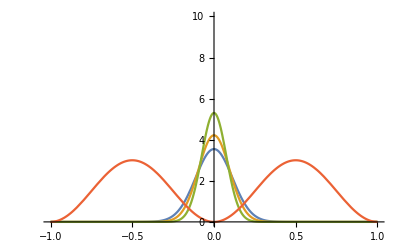

```mathematica
Plot[{(Subscript[ψ, wv][x,1,0])^2,(Subscript[ψ, wv][x,2,0])^2,(Subscript[ψ, wv][x,5,0])^2,3-3 Cos[x π]^2},{x,-1,1},
PlotRange-> {{-1,1},{0,10}}]
```

```mathematica
ItoEr[I_]:=√I μ / (1.24 10^3)
ErtoI[n_]:=hbar 1.24 10^3 n/μ^2
```

#### Scattering rates determined by integration of overlap with harmonic oscillator wave function with light from optical lattice

This is compared to for both the red and blue detuned lattices. All of these functions are determined by the lattice depth  “n” the relevant time scale/energy scale here is the recoil energy (E_rb) for the rubidium QGM or lithium (E_Li) QGM

```mathematica
Subscript[E, Rb]=2 π  1.24 10^3;
Subscript[E, Li]=2 π 25 10^3;
GSCBLUED2[n_]:=NIntegrate[n (1-Cos[x π]^2)  (Subscript[E, Rb])Subscript[γ, rb]/Subscript[δ, rb](Subscript[ψ, wv][x,n,0])^2,{x,-1,1}]
GSCBLUED1[n_]:=NIntegrate[n (1-Cos[x π]^2)(Subscript[E, Rb])Subscript[γ, rb]/(2 π 60 10^9)(Subscript[ψ, wv][x,n,0])^2,{x,-1,1}]
(*GSCRED[n_]:=NIntegrate[n (Cos[x π]^2) 1.24 10^3(680/532)^2 γ/δ(Subscript[ψ, wv][x,n,0])^2,{x,-1,1}]*)

GSCRED[n_]:=NIntegrate[n (Cos[x π]^2)( Subscript[E, Li])Subscript[γ, li]/Subscript[δ, li](Subscript[ψ, wv][x,n,0])^2,{x,-1,1}]
GSCBLUEDLI[n_]:=NIntegrate[n (1-Cos[x π]^2)( Subscript[E, Li])Subscript[γ, li]/Subscript[δ, li](Subscript[ψ, wv][x,n,0])^2,{x,-1,1}]
```

### Heating Calculations for Single Photon scattering events

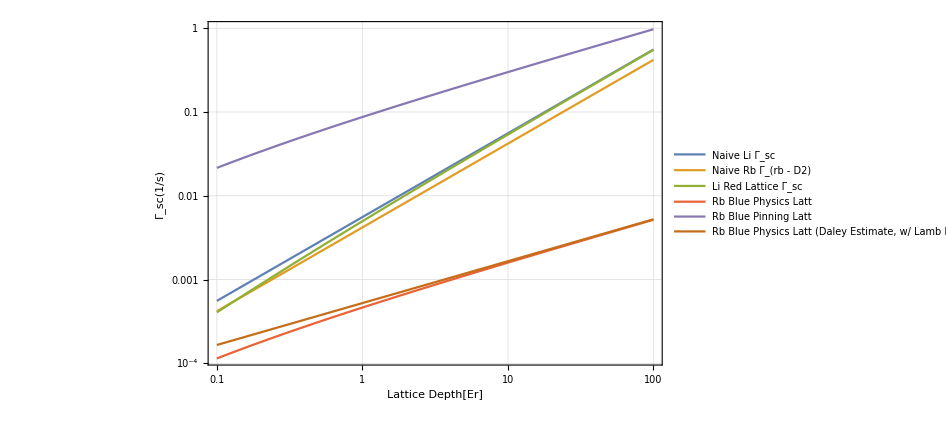

```mathematica
Subscript[λ, li]=670.992 10^-9;
Subscript[λ, laser] = 1064 10^-9;
Subscript[δ, li]= 2 π(Subscript[f, laser]-Subscript[f, li]);
Subscript[γ, li] = 2π 5.8724 10^6;

Subscript[λ, rb]=780.241209686 10^-9;
Subscript[λ, laser]=758 10^-9;
Subscript[γ, rb] = 2π  6.065 10^6;
Subscript[f, laser]=c/Subscript[λ, laser];
Subscript[f, rb]=c/Subscript[λ, rb];
Subscript[δ, rb]= 2 π(Subscript[f, laser]-Subscript[f, rb]);

(*I'm uncertain about the factor of 1/4 in the Daley paper... but It makes them agree at large depth*)
LogLogPlot[{Abs[Subscript[γ, li]/Subscript[δ, li] 2 π 24.9 10^3 x],
Abs[Subscript[γ, rb]/Subscript[δ, rb] 2 π 1.24 10^3 x],
Abs[GSCRED[x]],
Abs[GSCBLUED2[x]],
Abs[GSCBLUED1[x]],
Abs[Subscript[γ, rb]/Subscript[δ, rb] 2 π 1.24 10^3 x /4]( 4 x)^(-1/2)},
{x,0.1,100},
GridLines-> Automatic,
PlotStyle-> {Thick},
ImageSize-> 700,
Frame-> True,
FrameLabel-> {"Lattice Depth[Er]","Γ_sc(1/s)","Single Photon Scattering Rates for Li and Rb Exps"},
PlotLegends-> {"Naive Li Γ_sc","Naive Rb Γ_(rb - D2)","Li Red Lattice Γ_sc","Rb Blue Physics Latt","Rb Blue Pinning Latt","Rb Blue Physics Latt (Daley Estimate, w/ Lamb Dicke)"}]
```

```mathematica
GSCRED[10]/(2 π)
```

-0.00855785